# Liver slices MFA

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
OpenDBConnection[]
```

## Set paths

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

```mathematica
patientId="L002";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L002

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
net=First@OpenFLUXImport["liver-model_openflux.txt"];
```

Boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 35 boundary fluxes>

### Check against network from database

```mathematica
dbNet=NetworkFromDB[modelId];
```

```mathematica
TrueQ[net==dbNet]
```

True

### Get atom map from database

All atom transitions for reactions in model

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
atomMap=RenumberAtoms[RemoveUnreachable[net,atomMap]];
Length[atomMap]
```

90

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

35

Reactions without atom maps

```mathematica
Extract[Reactions[net],Position[AtomList/@atomMap,{}]]
```

{<Reaction ADK1>,<Reaction ATPS4m>,<Reaction ATPtm(rev)>,<Reaction CELLWORK>,<Reaction CRNtim>,<Reaction CYOOm>,<Reaction CYOR-u10m>,<Reaction GLYC_DEMAND>,<Reaction H2Oter>,<Reaction H2Otm(rev)>,<Reaction Htm2(rev)>,<Reaction NADH2-u10m>,<Reaction NADH_REDOX>,<Reaction NDPK1>,<Reaction NH4tm(rev)>,<Reaction O2tm>,<Reaction PIt2m>,<Reaction PIter>,<Reaction PPA>}

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTable[FileNameJoin[{lcmsDataDir,"L002",experimentId<>"_peakareas_ambiguous_met.tsv"}]];
```

```mathematica
measuredMetIds
```

{{glc-D},{ala-L},{arg-L},{asn-L},{asp-L},{Lcystin},{gln-L},{his-L},{leu-L},{ile-L},{lys-L},{met-L},{phe-L},{pro-L},{ser-L},{thr-L},{trp-L},{tyr-L},{val-L},{mal-L},{f6p,g1p,g6p},{r5p},{udpg},{creat},{orn},{citr-L},{gudac},{glyc3p},{akg},{succ},{glu-L},{gly}}

### Targets

Define targets from measured metabolites present in the model

```mathematica
targets=Cases[MetaboliteEMUs[atomMap],EMU[Metabolite[Alternatives@@Flatten[measuredMetIds],__],_]]
```

{<akg_c{(12345)}>,<akg_m{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<f6p_c{(123456)}>,<g1p_r{(123456)}>,<g6p_c{(123456)}>,<g6p_r{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>,<succ_m{(1234)}>}

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{asn-L,creat,gudac,his-L,ile-L,Lcystin,leu-L,lys-L,met-L,phe-L,pro-L,r5p,thr-L,trp-L,tyr-L,udpg,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

15

List of unique names for measurements, for use with GAMS

```mathematica
measuredMetNames=Map[ListToString[#,"__"]&,measuredMetIds]
```

{glc-D,ala-L,arg-L,asp-L,gln-L,ser-L,mal-L,f6p__g1p__g6p,orn,citr-L,glyc3p,akg,succ,glu-L,gly}

### EMU mixing matrix

Create (measurements x targets) mixing matrix

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[
Thread[{i,Flatten[Position[targets,EMU[Metabolite[Alternatives@@measuredMetIds⟦i⟧,_,_],_]]]}],
1]],
{i,Length[measuredMetIds]}],
{Length[measuredMetIds],Length[targets]}]
```

SparseArray[<26>, {15, 26}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

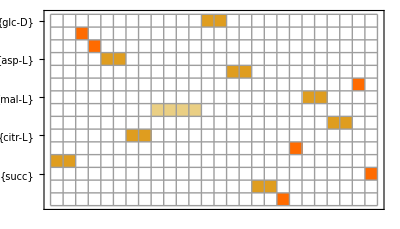

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetIds]],measuredMetIds}],None},Mesh->True]
```

List of measurement-target mappings

```mathematica
TableForm[Replace[
NonZeroIndices[emuMixing],
{i_,j_}:>{measuredMetNames⟦i⟧,targets⟦j⟧},{1}]]
```

glc-D | <glc-D_c{(123456)}>
glc-D | <glc-D_r{(123456)}>
ala-L | <ala-L_c{(123)}>
arg-L | <arg-L_c{(123456)}>
asp-L | <asp-L_c{(1234)}>
asp-L | <asp-L_m{(1234)}>
gln-L | <gln-L_c{(12345)}>
gln-L | <gln-L_m{(12345)}>
ser-L | <ser-L_c{(123)}>
mal-L | <mal-L_c{(1234)}>
mal-L | <mal-L_m{(1234)}>
f6p__g1p__g6p | <f6p_c{(123456)}>
f6p__g1p__g6p | <g1p_r{(123456)}>
f6p__g1p__g6p | <g6p_c{(123456)}>
f6p__g1p__g6p | <g6p_r{(123456)}>
orn | <orn_c{(12345)}>
orn | <orn_m{(12345)}>
citr-L | <citr-L_c{(123456)}>
citr-L | <citr-L_m{(123456)}>
glyc3p | <glyc3p_c{(123)}>
akg | <akg_c{(12345)}>
akg | <akg_m{(12345)}>
succ | <succ_m{(1234)}>
glu-L | <glu-L_c{(12345)}>
glu-L | <glu-L_m{(12345)}>
gly | <gly_c{(12)}>

### Sample annotations

For QC checks

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,1,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 24h,medium,13C,L002,1,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{fresh medium 0h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 0h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{,plasma,,L002,,human}}

Remove failed QC samples

```mathematica
Extract[sampleIds,Position[sampleInfo,{_,_,_,_,1,_}]]
```

{H_CE_LS_L_1,H_MS_LS_L_1}

```mathematica
Extract[sampleIds,Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]//TableForm
```

H_MS_U_FM24h_1
H_MS_U_FM24h_2
H_MS_U_FM24h_3

## Uptake/release data

### Concentration estimates from medium fold changes

This reflects net balance, not directional fluxes.

Fresh medium concentrations (M)

```mathematica
initConc=Rest[Import["C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\williams_E.txt","TSV"]];
initConc=Cases[initConc,{Alternatives@@(MetaboliteID/@InputMetabolites[net]),_}];
{measuredBoundaryIds,initConc}=Transpose[initConc];
measuredBoundaryIds=Partition[measuredBoundaryIds,1];
```

Fold changes fresh (incubated) medium, paired

```mathematica
Extract[sampleIds,
Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]
```

{H_MS_U_FM24h_1,H_MS_U_FM24h_2,H_MS_U_FM24h_3}

```mathematica
mediumFoldchange=Block[{metIndex,freshIndex,spentIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"12C",_,Except[1],_}]];
Map[First,measuredMIDs⟦metIndex,spentIndex,1⟧,{2}]/Map[First,measuredMIDs⟦metIndex,freshIndex,1⟧,{2}]];
```

```mathematica
TableForm[mediumFoldchange,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.66969 | 0.666832 | 0.656659
{arg-L} | 0.644172 | 0.902525 | 1.27053
{asp-L} | 0.677637 | 0.626805 | 0.710851
{gln-L} | 0.750615 | 0.676972 | 0.715755
{gly} | 0.748682 | 0.672288 | 0.594964
{ser-L} | 0.687248 | 0.624775 | 0.588538
{glc-D} | 0.886057 | 0.835328 | 0.843241

Convert to concentration differences

```mathematica
mediumConcDiff=initConc*(mediumFoldchange-1);
```

In um

```mathematica
TableForm[mediumConcDiff*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -333.614 | -336.5 | -346.774
{arg-L} | -84.3313 | -23.1015 | 64.1155
{asp-L} | -72.8541 | -84.342 | -65.3477
{gln-L} | -498.771 | -646.055 | -568.491
{gly} | -167.629 | -218.584 | -270.159
{ser-L} | -29.774 | -35.7214 | -39.1712
{glc-D} | -1264.77 | -1827.86 | -1740.02

### As mean +/- std dev

```mathematica
mediumConcDiffMean=Mean/@mediumConcDiff;
```

```mathematica
mediumConcDiffSD=StandardDeviation/@mediumConcDiff;
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944

### Add concentrations from clinical chemistry

Add lactate estimate (rough)

```mathematica
AppendTo[measuredBoundaryIds,{"lac-L"}];
AppendTo[mediumConcDiffMean,Mean[{1.0,1.5}]*0.001];
AppendTo[mediumConcDiffSD,StandardDeviation[{1.0,1.5}]*0.001];
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944
{lac-L} | 1250. | 353.553

### Calculate fluxes

Convert to fluxes (positive = release)

```mathematica
mediumVolume=0.0013;
cultureTime=24;
```

In nmol / h

```mathematica
TableForm[
Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*mediumVolume/cultureTime*10^9,
TableHeadings->{measuredBoundaryIds,{"mean","stddev"}}]
```

| mean | stddev
{ala-L} | -18.3605 | 0.374686
{arg-L} | -0.782118 | 4.04092
{asp-L} | -4.01815 | 0.518182
{gln-L} | -30.9349 | 3.99084
{gly} | -11.8511 | 2.77687
{ser-L} | -1.88981 | 0.257487
{glc-D} | -87.2563 | 16.4095
{lac-L} | 67.7083 | 19.1508

TODO: these values should constrain the difference of _IN and _OUT fluxes. We could have a linear transform of fluxes, similar to EMU mixing

For now we pick the flux to constrain according to sign

```mathematica
measuredBoundaryFluxeNames=Table[
measuredBoundaryIds⟦i⟧<>If[mediumConcDiffMean⟦i⟧<0,"_IN","_OUT"],
{i,Length[measuredBoundaryIds]}]
```

{ala-L_IN,arg-L_IN,asp-L_IN,gln-L_IN,gly_IN,ser-L_IN,glc-D_IN,lac-L_OUT}

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{90,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

77

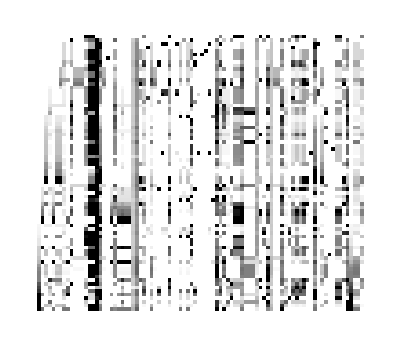

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]
```

{{<Reaction ACONTm(rev)>,cit_m <=> icit_m},{<Reaction ASPTAm(rev)>,glu-L_m + oaa_m <=> akg_m + asp-L_m},{<Reaction ATPtm(rev)>,adp_c + atp_m <=> adp_m + atp_c},{<Reaction G6Pter(rev)>,g6p_c <=> g6p_r},{<Reaction GHMT2r(rev)>,ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c},{<Reaction GLUNm(rev)>,gln-L_m + h2o_m <=> glu-L_m + nh4_m},{<Reaction ICDHxm(rev)>,icit_m + nad_m <=> akg_m + co2_m + nadh_m},{<Reaction LDH_L(rev)>,h_c + nadh_c + pyr_c <=> lac-L_c + nad_c},{<Reaction MDHm(rev)>,mal-L_m + nad_m <=> h_m + nadh_m + oaa_m},{<Reaction PYRt2m(rev)>,pyr_c <=> pyr_m}}

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[energy,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[pi,Output,Boundary]}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

956

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[126,<glu-L_m{(12)}>,<glu-L_c{(12)}>,1],EMUReaction[97,<g1p_r{(3)}>,<g6p_r{(3)}>,1],EMUReaction[63,<gln-L_m{(124)}>,<glu-L_m{(124)}>,1],EMUReaction[2,<ac_i{(1)}>,<ac_c{(1)}>,1],EMUReaction[89,<pyr_m{(12)}>,<oaa_m{(12)}>,1],EMUReaction[104,<3php_c{(2)}>,<pser-L_c{(2)}>,1],EMUReaction[81,<2mop_m{(123)}>,<ppcoa_m{(123)}>,1],EMUReaction[60,<glc-D_r{(23)}>,<glc-D_c{(23)}>,1],EMUReaction[104,<glu-L_c{(13)}>,<akg_c{(13)}>,1],EMUReaction[81,<2mop_m{(2)}>,<ppcoa_m{(3)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

487

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["glc-D",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

glc-D_IN | <glc-D_i{(1)}> | <glc-D_c{(1)}>
GLCter_f | <glc-D_r{(1)}> | <glc-D_c{(1)}>
glc-D_IN | <glc-D_i{(2)}> | <glc-D_c{(2)}>
GLCter_f | <glc-D_r{(2)}> | <glc-D_c{(2)}>
glc-D_IN | <glc-D_i{(3)}> | <glc-D_c{(3)}>
GLCter_f | <glc-D_r{(3)}> | <glc-D_c{(3)}>
glc-D_IN | <glc-D_i{(4)}> | <glc-D_c{(4)}>
GLCter_f | <glc-D_r{(4)}> | <glc-D_c{(4)}>
glc-D_IN | <glc-D_i{(5)}> | <glc-D_c{(5)}>
GLCter_f | <glc-D_r{(5)}> | <glc-D_c{(5)}>
glc-D_IN | <glc-D_i{(6)}> | <glc-D_c{(6)}>
GLCter_f | <glc-D_r{(6)}> | <glc-D_c{(6)}>
glc-D_IN | <glc-D_i{(12)}> | <glc-D_c{(12)}>
GLCter_f | <glc-D_r{(12)}> | <glc-D_c{(12)}>
glc-D_IN | <glc-D_i{(23)}> | <glc-D_c{(23)}>
GLCter_f | <glc-D_r{(23)}> | <glc-D_c{(23)}>
glc-D_IN | <glc-D_i{(45)}> | <glc-D_c{(45)}>
GLCter_f | <glc-D_r{(45)}> | <glc-D_c{(45)}>
glc-D_IN | <glc-D_i{(56)}> | <glc-D_c{(56)}>
GLCter_f | <glc-D_r{(56)}> | <glc-D_c{(56)}>
glc-D_IN | <glc-D_i{(123)}> | <glc-D_c{(123)}>
GLCter_f | <glc-D_r{(123)}> | <glc-D_c{(123)}>
glc-D_IN | <glc-D_i{(456)}> | <glc-D_c{(456)}>
GLCter_f | <glc-D_r{(456)}> | <glc-D_c{(456)}>
glc-D_IN | <glc-D_i{(123456)}> | <glc-D_c{(123456)}>
GLCter_f | <glc-D_r{(123456)}> | <glc-D_c{(123456)}>
G6PPer_f | <g6p_r{(1)}> | <glc-D_r{(1)}>
G6PPer_f | <g6p_r{(2)}> | <glc-D_r{(2)}>
G6PPer_f | <g6p_r{(3)}> | <glc-D_r{(3)}>
G6PPer_f | <g6p_r{(4)}> | <glc-D_r{(4)}>
G6PPer_f | <g6p_r{(5)}> | <glc-D_r{(5)}>
G6PPer_f | <g6p_r{(6)}> | <glc-D_r{(6)}>
G6PPer_f | <g6p_r{(12)}> | <glc-D_r{(12)}>
G6PPer_f | <g6p_r{(23)}> | <glc-D_r{(23)}>
G6PPer_f | <g6p_r{(45)}> | <glc-D_r{(45)}>
G6PPer_f | <g6p_r{(56)}> | <glc-D_r{(56)}>
G6PPer_f | <g6p_r{(123)}> | <glc-D_r{(123)}>
G6PPer_f | <g6p_r{(456)}> | <glc-D_r{(456)}>
G6PPer_f | <g6p_r{(123456)}> | <glc-D_r{(123456)}>

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 211 internals, 39 substrates, 0 condensations >
2 | <EMUEquation (2), 146 internals, 25 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

### Specify input isotopomers (tracers)

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID["substrate-distributions.txt"]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.98}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.98}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.98}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.98}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.98}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.98}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.98}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.98}]}

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

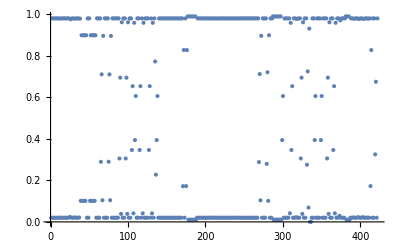
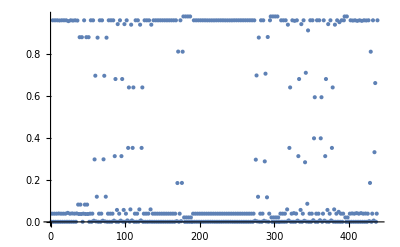
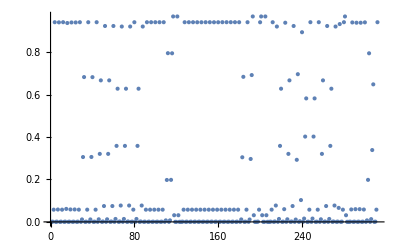
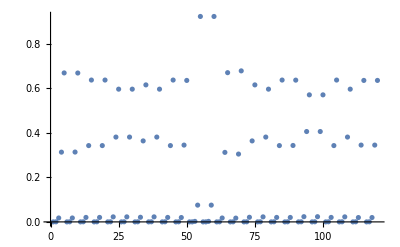
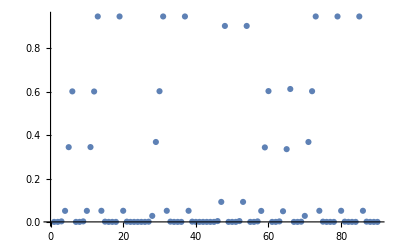
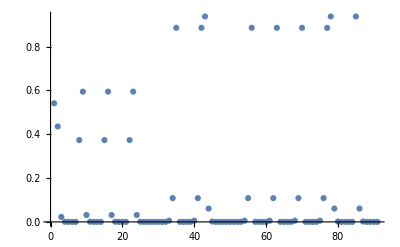

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],"mathematica","gams"}]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.01;
```

```mathematica
Directory[]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

### Generate optimization model

MIDs to fit

```mathematica
midsToFit=Block[{sampleIndex},
sampleIndex=Flatten[Position[sampleInfo,{"tissue slice 24h",_,"13C",_,Except[1],_}]];
Map[First[MIDNormalize[#]]&,measuredMIDs⟦All,sampleIndex⟧,{2}]];
```

Export model file

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes *)
measuredBoundaryFluxeNames,Abs[mediumConcDiffMean*mediumVolume/cultureTime*10^9],mediumConcDiffSD*mediumVolume/cultureTime*10^9,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
RandomFluxState[10]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams\liver-model.gms

### Run GAMS

From command line ...

### Import GAMS solutions

#### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<22>, {15, 26}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

glc-D | <glc-D_c{(123456)}> | 0.998265
glc-D | <glc-D_r{(123456)}> | 0.00173529
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 1.
asp-L | <asp-L_c{(1234)}> | 0.42954
asp-L | <asp-L_m{(1234)}> | 0.57046
gln-L | <gln-L_c{(12345)}> | 0.561337
gln-L | <gln-L_m{(12345)}> | 0.438663
ser-L | <ser-L_c{(123)}> | 1.
mal-L | <mal-L_c{(1234)}> | 0.42935
mal-L | <mal-L_m{(1234)}> | 0.57065
f6p__g1p__g6p | <f6p_c{(123456)}> | 0.241326
f6p__g1p__g6p | <g1p_r{(123456)}> | 0.758674
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glyc3p | <glyc3p_c{(123)}> | 1.
akg | <akg_c{(12345)}> | 1.
succ | <succ_m{(1234)}> | 1.
glu-L | <glu-L_c{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.

#### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

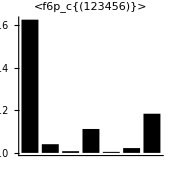
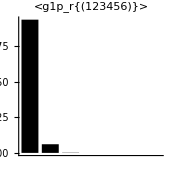
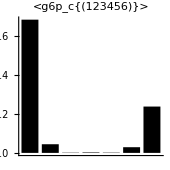
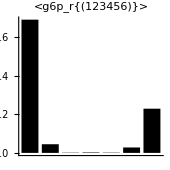
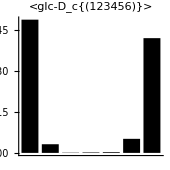
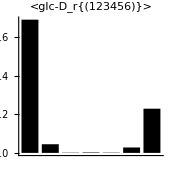

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["f6p"|"g6p"|"g1p"|"glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

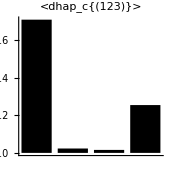
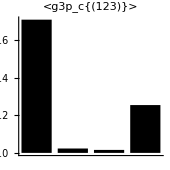
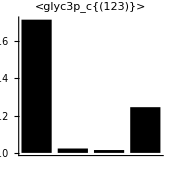

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p"|"dhap"|"glyc3p",__],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

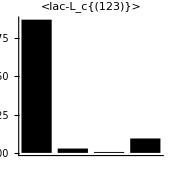

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["lac-L",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

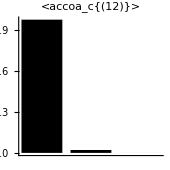
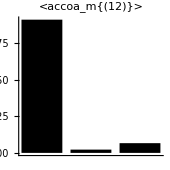

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

#### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixing;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

Compare fitted MIDs (gray) with measured (black)

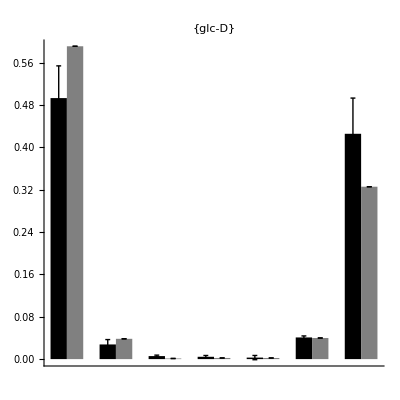
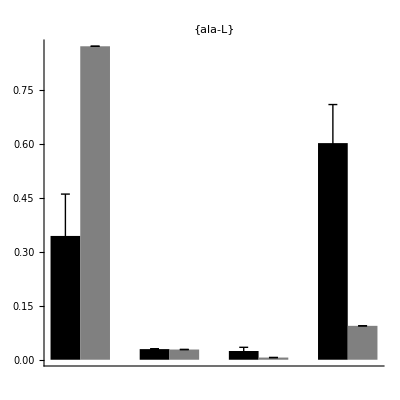
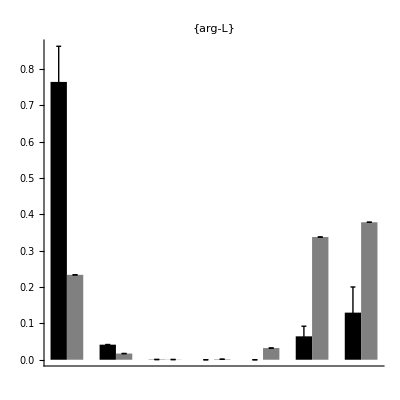
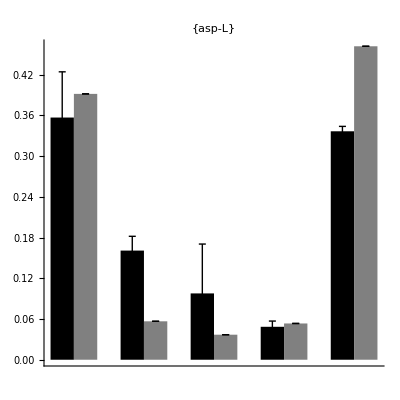
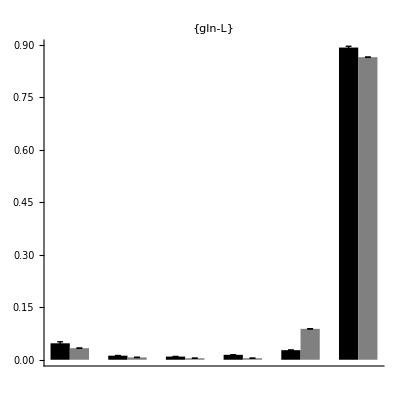
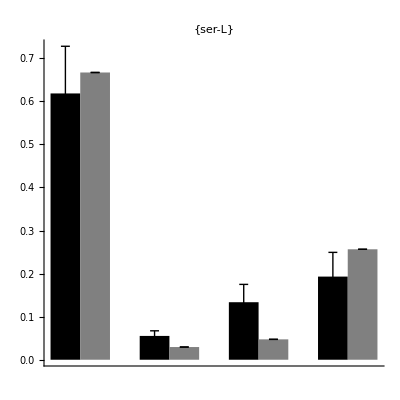
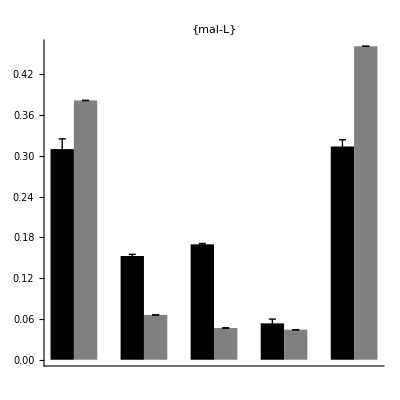
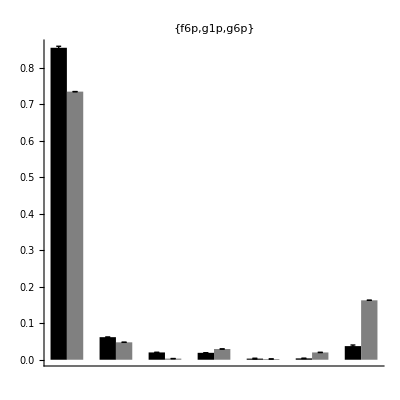

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetIds⟦i⟧],
{i,Length[measuredMetIds]}]
```

Scatter plot of all fitted MIDs

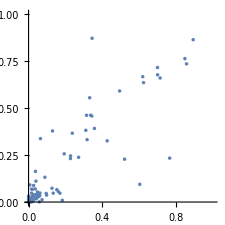

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

#### Fluxes

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 89 reactions, 35 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 0.001 | 0. | 0.001
<Reaction ACITL> | 0.001 | 0. | 0.001
<Reaction ACOAHi> | 0.001 | 0. | 0.001
<Reaction ACONTm(rev)> | 127.249 | 0.001 | 127.248
<Reaction ACRNtm> | 39.4248 | 0. | 39.4248
<Reaction ACS> | 39.4248 | 0. | 39.4248
<Reaction ADK1> | 39.4279 | 0. | 39.4279
<Reaction AKGDm(rev)> | 10000. | 9902.58 | 97.4213
<Reaction AKGtm(rev)> | 0.001 | 29.944 | -29.943
<Reaction ALATA_L> | 183.467 | 0. | 183.467
<Reaction ARGN> | 0.00316553 | 0. | 0.00316553
<Reaction ARGSL> | 0.00316553 | 0. | 0.00316553
<Reaction ARGSS> | 0.00316553 | 0. | 0.00316553
<Reaction ASPTA(rev)> | 10000. | 10000. | 0.001
<Reaction ASPTAm(rev)> | 0.002 | 0.001 | 0.001
<Reaction ASPtm> | 0.001 | 0. | 0.001
<Reaction ATPS4m> | 1171.22 | 0. | 1171.22
<Reaction ATPtm(rev)> | 1238.82 | 0.001 | 1238.82
<Reaction CBPSam> | 0.00316553 | 0. | 0.00316553
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 0.001 | 0. | 0.001
<Reaction CO2tm(rev)> | 7995.12 | 8277.79 | -282.667
<Reaction CRNtim> | 39.4248 | 0. | 39.4248
<Reaction CSm> | 127.249 | 0. | 127.249
<Reaction CSNATm> | 39.4248 | 0. | 39.4248
<Reaction CSNATr> | 39.4248 | 0. | 39.4248
<Reaction CYOOm> | 253.729 | 0. | 253.729
<Reaction CYOR-u10m> | 507.459 | 0. | 507.459
<Reaction ENO(rev)> | 5.02387 | 5.02387 | 0.
<Reaction FBA(rev)> | 9965.81 | 9945.65 | 20.1657
<Reaction FBP> | 1080.76 | 0. | 1080.76
<Reaction FUMm> | 97.4254 | 0. | 97.4254
<Reaction FUMtm> | 0.00316553 | 0. | 0.00316553
<Reaction G3PD1(rev)> | 4162.76 | 4049.57 | 113.193
<Reaction G6PPer> | 146.737 | 0. | 146.737
<Reaction G6Pter> | 67.0916 | 0. | 67.0916
<Reaction GAPD(rev)> | 156.973 | 3.4487 | 153.525
<Reaction GHMT2r(rev)> | 11.5036 | 11.5036 | 0.
<Reaction GLCter> | 0.001 | 0. | 0.001
<Reaction GLNtm> | 30.6349 | 0. | 30.6349
<Reaction GLUDxm(rev)> | 0.115737 | 0.001 | 0.114737
<Reaction GLUNm(rev)> | 166.213 | 135.578 | 30.6349
<Reaction GLUt2m(rev)> | 9969.48 | 10000. | -30.5192
<Reaction GLYCOGEN_BREAKer> | 79.6456 | 0. | 79.6456
<Reaction GLYK> | 113.193 | 0. | 113.193
<Reaction GTHS> | 12.1034 | 0. | 12.1034
<Reaction H2Oter> | 146.737 | 0. | 146.737
<Reaction H2Otm(rev)> | 0.001 | 1393.43 | -1393.43
<Reaction HCO3Em> | 29.8282 | 0. | 29.8282
<Reaction HEX1> | 87.2573 | 0. | 87.2573
<Reaction Htm2(rev)> | 0.001 | 1296.81 | -1296.81
<Reaction ICDHxm(rev)> | 127.249 | 0.001 | 127.248
<Reaction LDH_L(rev)> | 65.8208 | 0.001 | 65.8198
<Reaction MALtm> | 0.001 | 0. | 0.001
<Reaction MDH> | 0.001 | 0. | 0.001
<Reaction MDHm(rev)> | 97.4274 | 0.001 | 97.4264
<Reaction MMEm> | 0.001 | 0. | 0.001
<Reaction MMMm> | 0.001 | 0. | 0.001
<Reaction MMSAD1m> | 0.001 | 0. | 0.001
<Reaction NADH2-u10m> | 410.037 | 0. | 410.037
<Reaction NADH_REDOX> | 354.422 | 0. | 354.422
<Reaction NDPK1> | 0.001 | 0. | 0.001
<Reaction NH4tm(rev)> | 0.001 | 30.7475 | -30.7465
<Reaction O2tm> | 253.729 | 0. | 253.729
<Reaction OCBTm> | 0.00316553 | 0. | 0.00316553
<Reaction ORNt4m> | 0.00316553 | 0. | 0.00316553
<Reaction PCm> | 29.8241 | 0. | 29.8241
<Reaction PDHm> | 87.8247 | 0. | 87.8247
<Reaction PEPCK> | 0.001 | 0. | 0.001
<Reaction PFK> | 1100.93 | 0. | 1100.93
<Reaction PGCD> | 153.525 | 0. | 153.525
<Reaction PGI(rev)> | 21.1488 | 0.983133 | 20.1657
<Reaction PGK(rev)> | 156.973 | 3.4487 | 153.525
<Reaction PGM(rev)> | 60.1241 | 60.1241 | 0.
<Reaction PGMTer> | 79.6456 | 0. | 79.6456
<Reaction PIt2m> | 1238.82 | 0. | 1238.82
<Reaction PIter> | 67.0916 | 0. | 67.0916
<Reaction PPA> | 39.4279 | 0. | 39.4279
<Reaction PPCOACm> | 0.001 | 0. | 0.001
<Reaction PROTDEG_ALA> | 165.102 | 0. | 165.102
<Reaction PROTDEG_ARG> | 0.001 | 0. | 0.001
<Reaction PSERT> | 153.525 | 0. | 153.525
<Reaction PSP_L> | 153.525 | 0. | 153.525
<Reaction PYK> | 0.001 | 0. | 0.001
<Reaction PYRt2m(rev)> | 117.65 | 0.001 | 117.649
<Reaction SERHL> | 0.001 | 0. | 0.001
<Reaction SUCD1m> | 97.4223 | 0. | 97.4223
<Reaction SUCOASm> | 97.4223 | 0. | 97.4223
<Reaction TPI(rev)> | 10000. | 9866.64 | 133.359

```mathematica
MetaboliteProducers[net,Metabolite["glc-D","Cytosol","Uptake"]]
```

{{<Reaction GLCter>,1}}

Boundary fluxes vs. measured

```mathematica
TableForm[
Transpose[{
BoundaryFlux[fluxGams],
BoundaryFluxNames[bnet]/.Append[Thread[Rule[measuredBoundaryFluxeNames,Abs[mediumConcDiffMean*mediumVolume/cultureTime*10^9]]],
_String->""]}],
TableHeadings->{BoundaryFluxNames[bnet],{"Fitted","Measured"}}]
```

| Fitted | Measured
2mop_IN | 0.001 | 
ac_IN | 39.4238 | 
ala-L_IN | 18.3641 | 18.3605
arg-L_IN | 0.00298382 | 0.782118
asp-L_IN | 4.01853 | 4.01815
co2_IN | 1379.6 | 
energy_IN | 0.001 | 
glc-D_IN | 87.2563 | 87.2563
gln-L_IN | 30.6349 | 30.9349
glucys_IN | 12.1034 | 
gly_IN | 12.1034 | 11.8511
glyc_IN | 113.193 | 
glycogen_IN | 79.6456 | 
h2o_IN | 27.0279 | 
h_IN | 10.782 | 
nh4_IN | 27.278 | 
o2_IN | 253.729 | 
pi_IN | 0.001 | 
prot_ala_IN | 165.102 | 
prot_arg_IN | 0.001 | 
ser-L_IN | 1.88964 | 1.88981
arg-L_OUT | 0.00398382 | 
asp-L_OUT | 4.01536 | 
co2_OUT | 1662.27 | 
energy_OUT | 0.002 | 
glc-D_OUT | 146.736 | 
glu-L_OUT | 60.4622 | 
gthrd_OUT | 12.1034 | 
h2o_OUT | 0.001 | 
h_OUT | 775.732 | 
lac-L_OUT | 65.8198 | 67.7083
nh4_OUT | 58.0255 | 
pi_OUT | 0.001 | 
ser-L_OUT | 155.413 | 
urea_OUT | 0.00316553 |